```mathematica
master = D[Y[x],x]==-svn2/(x s H)(Y[x]^2/Yeq^2-1);
numbers={g->170,
gs->170.,
M0->10^18,
m->1000,
α->0.1,
gX->16
};
```

```mathematica
rules1={
H->√((g π^2)/90)T^2/(Mpl/"sqrt8π"),
s->(2 π^2)/45 gs T^3,
T->m/x,
svn2->gX^2/(2 π^4)m^6 x^-2 BesselK[1,m/T]^2 σ0 ,
Yeq->gX/("2πsq")m^2 T BesselK[2,m/T]/s
};
ours=master//.rules1
```

Y'[x]==-(135 √(5/2) gX^2 m Mpl x^2 σ0 BesselK[1,x]^2 (-1+(4 (2πsq)^2 gs^2 π^4 Y[x]^2)/(2025 gX^2 x^4 BesselK[2,x]^2)))/(2 sqrt8π √g gs π^7)

```mathematica
abbr={
Mpl->RX/(gX/(√g) m σ0),
"sqrt8π"->(2 π^2)/45/(√(π^2/90) k1 ),
"2πsq"->1/(k2 (2 π^2)/45)√(π/2),
BesselK[2,x_]:>x^-2 F2[x],
BesselK[1,x_]:>x^-1 F1[x],
2025->32 k2^2 π^7,
F2[Exp[ϕ_]]:>G2[ϕ],
F1[Exp[ϕ_]]:>G1[ϕ]
};
abbrb={
RX->gX m Mpl σ0/√g,
k1->2 π^2/45/(√(π^2/90)√(8π)),
k2->(1/(2 π^2))/(2 π^2/45)√(π/2)
};
abbr//.abbrb
```

{Mpl→Mpl,sqrt8π→2 √(2 π),2πsq→2 π^2,BesselK[2,x_]:>F2[x]/x^2,BesselK[1,x_]:>F1[x]/x,2025→2025,F2[ⅇ^ϕ_]:>G2[ϕ],F1[ⅇ^ϕ_]:>G1[ϕ]}

```mathematica
ours2=ours//.abbr//FullSimplify[#,{g>0,k1>0,gs>0,gX>0,k2>0,"2π^2/45">0}]&;
```

```mathematica
ours2//.{
Y'[x]->D[√(2/π)gX/gs k2f[ϕ],ϕ]D[Log[x],x],
Y[x]->√(2/π)gX/gs k2f[ϕ],
x->Exp[ϕ]
}/.abbr//FullSimplify;
Solve[%//.abbr,f'[ϕ]]//FullSimplify[#,{x>0,ϕ∈Reals,G2[ϕ]>0,BesselK[1,x]≠0}]&
```

{{f'[ϕ]→(2 ⅇ^ϕ k1 k2 √(2/π) RX G1[ϕ]^2 (-f[ϕ]^2+G2[ϕ]^2))/G2[ϕ]^2}}

## Functions

```mathematica
Series[(x^2 BesselK[2,x])/(√(π/2)Exp[-x] x^(3/2)),{x,∞,2}]//FullSimplify
Series[x^2 BesselK[2,x],{x,0,6}]//Normal//FullSimplify
Normal[%]/.x->Exp[ϕ]//FullSimplify[#,ϕ>0]&
Series[(x BesselK[1,x])/(√(π/2)Exp[-x] x^(1/2)),{x,∞,2}]//FullSimplify
Series[x BesselK[1,x],{x,0,6}]//Normal//FullSimplify
Normal[%]/.x->Exp[ϕ]//FullSimplify[#,ϕ>0]&
```

1+15/(8 x)+105/(128 x^2)+O[1/x]^3

2-x^2/2+(x^6 (17-12 EulerGamma+Log[4096]-12 Log[x]))/1152+1/32 x^4 (3-4 EulerGamma+Log[16]-4 Log[x])

2-ⅇ^(2 ϕ)/2+1/32 ⅇ^(4 ϕ) (3-4 EulerGamma-4 ϕ+Log[16])+(ⅇ^(6 ϕ) (17-12 EulerGamma-12 ϕ+Log[4096]))/1152

1+3/(8 x)-15/(128 x^2)+O[1/x]^3

1+1/4 x^2 (-1+2 EulerGamma-Log[4]+2 Log[x])+(x^6 (-5+3 EulerGamma-Log[8]+3 Log[x]))/1152+1/64 x^4 (-5+4 EulerGamma-4 Log[2]+4 Log[x])

1+1/64 ⅇ^(4 ϕ) (-5+4 EulerGamma+4 ϕ-4 Log[2])+1/4 ⅇ^(2 ϕ) (-1+2 EulerGamma+2 ϕ-Log[4])+(ⅇ^(6 ϕ) (-5+3 EulerGamma+3 ϕ-Log[8]))/1152

```mathematica
G2[ϕ_]/;ϕ<-4:=2-ⅇ^(2 ϕ)/2+1/32 ⅇ^(4 ϕ) (3-4 EulerGamma-4 ϕ+Log[16])+(ⅇ^(6 ϕ) (17-12 EulerGamma-12 ϕ+Log[4096]))/1152
G2[ϕ_]:=BesselK[2,Exp[ϕ]]Exp[2ϕ]
G1[ϕ_]/;ϕ<-4:=1+1/4 x^2 (-1+2 EulerGamma-Log[4]+2 Log[x])+(x^6 (-5+3 EulerGamma-Log[8]+3 Log[x]))/1152+1/64 x^4 (-5+4 EulerGamma-4 Log[2]+4 Log[x])
G1[ϕ_]:=BesselK[1,Exp[ϕ]]Exp[ϕ]
```

{f'[ϕ]==(1000 ⅇ^-ϕ BesselK[1,ⅇ^ϕ]^2 (ⅇ^(4 ϕ) BesselK[2,ⅇ^ϕ]^2-f[ϕ]^2))/(BesselK[2,ⅇ^ϕ]^2),f[-50]==3}

{{f→InterpolatingFunction[…]}}

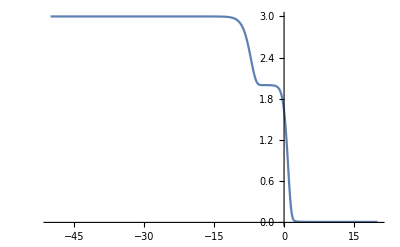

```mathematica
{min,max,start,R}={-50,20,3,1000};
{f'[ϕ]==(R ⅇ^ϕ  G1[ϕ]^2 (-f[ϕ]^2+G2[ϕ]^2))/G2[ϕ]^2,f[min]==start}
sol=NDSolve[%,f,{ϕ,min,max}]
Plot[f[ϕ]/.sol,{ϕ,min,max},PlotRange->All]
```

```mathematica
Finf[Rin_]:=Module[{},
{min,max,start,R}={-50,50,3,Rin};
sol=NDSolve[{f'[ϕ]==(R ⅇ^ϕ  G1[ϕ]^2 (-f[ϕ]^2+G2[ϕ]^2))/G2[ϕ]^2,f[min]==start},f,{ϕ,min,max}];
f[max/1.01]/.sol[[1]]]
```

{{1/1125899906842624,3.},{1/562949953421312,3.},{1/281474976710656,3.},{1/140737488355328,3.},{1/70368744177664,3.},{1/35184372088832,3.},{1/17592186044416,3.},{1/8796093022208,3.},{1/4398046511104,3.},{1/2199023255552,3.},{1/1099511627776,3.},{1/549755813888,3.},{1/274877906944,3.},{1/137438953472,3.},{1/68719476736,3.},{1/34359738368,3.},{1/17179869184,3.},{1/8589934592,3.},{1/4294967296,3.},{1/2147483648,3.},{1/1073741824,3.},{1/536870912,3.},{1/268435456,3.},{1/134217728,3.},{1/67108864,3.},{1/33554432,3.},{1/16777216,3.},{1/8388608,3.},{1/4194304,3.},{1/2097152,3.},{1/1048576,3.},{1/524288,2.99999},{1/262144,2.99998},{1/131072,2.99997},{1/65536,2.99993},{1/32768,2.99987},{1/16384,2.99974},{1/8192,2.99948},{1/4096,2.99896},{1/2048,2.99792},{1/1024,2.99585},{1/512,2.99171},{1/256,2.98347},{1/128,2.96714},{1/64,2.93505},{1/32,2.87305},{1/16,2.75715},{1/8,2.55322},{1/4,2.23002},{1/2,1.79413},{1,1.3187},{2,0.903145},{4,0.591892},{8,0.372106},{16,0.225003},{32,0.132217},{64,0.0760653},{128,0.0430519},{256,0.0240527},{512,0.013297},{1024,0.00728699},{2048,0.00396405},{4096,0.00214284},{8192,0.00115215},{16384,0.0006165},{32768,0.00032856},{65536,0.000174412},{131072,0.0000923226},{262144,0.0000487169},{524288,0.0000256552},{1048576,0.0000134433},{2097152,7.06251×10^-6},{4194304,3.67824×10^-6},{8388608,1.93011×10^-6},{16777216,1.00509×10^-6},{33554432,5.23131×10^-7},{67108864,2.66468×10^-7},{134217728,1.37212×10^-7},{268435456,7.12348×10^-8},{536870912,3.68689×10^-8},{1073741824,1.86874×10^-8}}

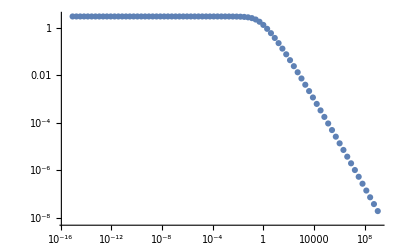

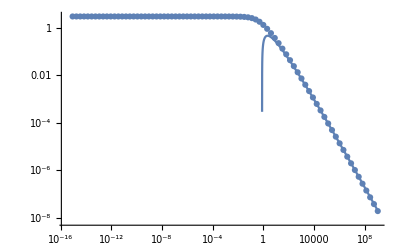

```mathematica
Table[{2^i,Finf[2^i]},{i,-50,30}]
plot=ListLogLogPlot[%]
Show[plot,LogLogPlot[Log[√(π/2)x]/x,{x,2^-50,2^30}]]
```